```mathematica
Simplify@D[4ϵ((σ/r)^12-(σ/r)^6),r]
```

(24 ϵ σ^6 (r^6-2 σ^6))/r^13

-Graphics3D-

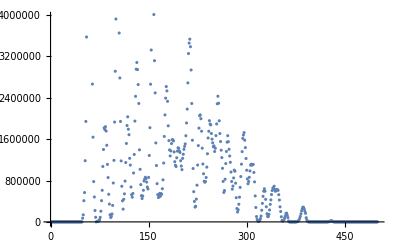

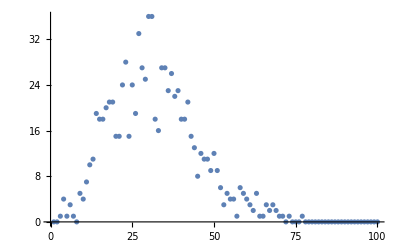

```mathematica
scaleFactor=10^9;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/positions.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
velocities= ReadList["~/phd-stuff/courses/astrid_sim/velocities.txt",Number,RecordLists->False];
sortvelocities=Sort[Flatten@velocities];
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->False];
ListPlot[rdf]
veldist = ReadList["~/phd-stuff/courses/astrid_sim/speeddist.txt",Number,RecordLists->False];
ListPlot[veldist]
```

```mathematica
Table[{k,initPositions[[k]]},{k,1,Length[initPositions]}];
numvel=Table[{k,velocities[[k]]},{k,1,Length[velocities]}];
Sort[numvel,#1[[2]]>#2[[2]]&]
```

{{773,2.07171×10^39},{659,2.07171×10^39},{301,1.68516×10^26},{28,1.68516×10^26},{789,2.61457×10^25},{326,2.61457×10^25},{711,1.00162×10^25},{193,1.00162×10^25},{651,9.01735×10^24},{318,9.01735×10^24},{694,4.18903×10^24},{372,4.18903×10^24},{415,3.72802×10^24},{48,3.72802×10^24},{401,1.99021×10^23},{357,1.99021×10^23},{854,1.63944×10^23},{69,1.63944×10^23},{779,1.08172×10^23},{726,1.08172×10^23},{367,6.11163×10^22},{264,6.11163×10^22},{542,3.88693×10^22},{404,3.88693×10^22},{695,2.11229×10^22},{58,2.11229×10^22},{287,1.78038×10^22},{25,1.78038×10^22},{839,1.17907×10^22},{409,1.17907×10^22},{669,3.20312×10^21},{450,3.20312×10^21},{829,1.11643×10^21},{166,1.11643×10^21},{654,1.09476×10^21},{109,1.09476×10^21},{554,1.07718×10^21},{153,1.07718×10^21},{710,8.81961×10^20},{591,8.81961×10^20},{50,7.98537×10^20},{738,7.68767×10^20},{567,6.19919×10^20},{222,6.19919×10^20},{78,5.23536×10^20},{144,5.23534×10^20},{720,4.59929×10^20},{348,4.59929×10^20},{741,4.27322×10^20},{107,4.27322×10^20},{765,4.11065×10^20},{416,4.11065×10^20},{515,3.25676×10^20},{446,3.25676×10^20},{471,3.09794×10^20},{229,3.09794×10^20},{563,2.39999×10^20},{45,2.39999×10^20},{436,2.05832×10^20},{136,2.05832×10^20},{852,1.36091×10^20},{786,1.36091×10^20},{753,1.06818×10^20},{210,1.06818×10^20},{239,9.02689×10^19},{22,9.02688×10^19},{304,6.88518×10^19},{732,6.13452×10^19},{225,6.04905×10^19},{606,6.04879×10^19},{481,4.69432×10^19},{733,4.66407×10^19},{235,4.11288×10^19},{171,4.11286×10^19},{93,3.43538×10^19},{29,3.43538×10^19},{219,3.00141×10^19},{251,3.00137×10^19},{226,2.95905×10^19},{757,2.781×10^19},{623,2.781×10^19},{680,1.91987×10^19},{231,1.91986×10^19},{635,1.36162×10^19},{767,1.16806×10^19},{794,1.16796×10^19},{430,9.42139×10^18},{157,9.42096×10^18},{55,8.90231×10^18},{145,8.90155×10^18},{573,8.50626×10^18},{7,8.50626×10^18},{825,8.09366×10^18},{609,8.09366×10^18},{807,7.92289×10^18},{276,7.92212×10^18},{424,7.43349×10^18},{65,7.43348×10^18},{216,6.97428×10^18},{3,6.97414×10^18},{466,6.57697×10^18},{593,6.57667×10^18},{791,6.42839×10^18},{220,6.42675×10^18},{451,6.25323×10^18},{188,6.2524×10^18},{488,5.69171×10^18},{129,5.69164×10^18},{199,5.58133×10^18},{579,5.58128×10^18},{176,5.01351×10^18},{63,5.01351×10^18},{647,3.7886×10^18},{849,3.71467×10^18},{641,3.71463×10^18},{709,3.36182×10^18},{27,3.36164×10^18},{163,2.9371×10^18},{772,2.93679×10^18},{833,2.76259×10^18},{388,2.76245×10^18},{762,2.60391×10^18},{405,2.60391×10^18},{396,2.36178×10^18},{771,2.36142×10^18},{248,2.34317×10^18},{413,2.34316×10^18},{177,2.33188×10^18},{477,2.33166×10^18},{6,2.21453×10^18},{795,2.21448×10^18},{668,2.19981×10^18},{334,2.19833×10^18},{505,2.19798×10^18},{501,2.17176×10^18},{60,2.04917×10^18},{190,2.04895×10^18},{824,1.94813×10^18},{716,1.94811×10^18},{701,1.79373×10^18},{343,1.79365×10^18},{775,1.65688×10^18},{273,1.65687×10^18},{148,1.50489×10^18},{621,1.50488×10^18},{751,1.50262×10^18},{577,1.49977×10^18},{858,9.15683×10^17},{135,9.15664×10^17},{519,8.38995×10^17},{255,8.3742×10^17},{380,7.50044×10^17},{455,7.49997×10^17},{205,7.19054×10^17},{576,7.18891×10^17},{203,7.12808×10^17},{336,7.12786×10^17},{755,6.53113×10^17},{731,6.53087×10^17},{156,5.60822×10^17},{77,5.60822×10^17},{323,5.41518×10^17},{814,5.28727×10^17},{513,5.28478×10^17},{95,5.24963×10^17},{420,5.10779×10^17},{820,5.10717×10^17},{666,4.72663×10^17},{508,4.72663×10^17},{590,4.53166×10^17},{674,4.52524×10^17},{507,4.1785×10^17},{353,4.17384×10^17},{476,4.12211×10^17},{42,4.11824×10^17},{683,4.0085×10^17},{214,3.97128×10^17},{862,3.97098×10^17},{457,3.90051×10^17},{365,3.71943×10^17},{610,3.71275×10^17},{780,3.71254×10^17},{603,3.50771×10^17},{690,3.5077×10^17},{713,3.34263×10^17},{124,3.33276×10^17},{16,3.31201×10^17},{438,3.31171×10^17},{553,3.21754×10^17},{797,3.21226×10^17},{521,3.20732×10^17},{860,3.01311×10^17},{337,2.97529×10^17},{851,2.97524×10^17},{447,2.95498×10^17},{319,2.94959×10^17},{335,2.90273×10^17},{468,2.90255×10^17},{624,2.86148×10^17},{73,2.77393×10^17},{834,2.73445×10^17},{411,2.6693×10^17},{368,2.64434×10^17},{13,2.64291×10^17},{125,2.56302×10^17},{83,2.56302×10^17},{119,2.39744×10^17},{541,2.39597×10^17},{84,2.37176×10^17},{601,2.37055×10^17},{792,2.31778×10^17},{206,2.31102×10^17},{804,2.2445×10^17},{681,2.23966×10^17},{80,2.23945×10^17},{472,2.23822×10^17},{570,1.90593×10^17},{597,1.90188×10^17},{617,1.79234×10^17},{311,1.7804×10^17},{844,1.77973×10^17},{232,1.71109×10^17},{632,1.70897×10^17},{853,1.58022×10^17},{356,1.57985×10^17},{850,1.49752×10^17},{522,1.49051×10^17},{503,1.37594×10^17},{537,1.37578×10^17},{379,1.27431×10^17},{633,1.25181×10^17},{538,1.25175×10^17},{97,1.09408×10^17},{31,1.08507×10^17},{608,1.06671×10^17},{8,1.06569×10^17},{86,1.06237×10^17},{616,1.06145×10^17},{535,9.18602×10^16},{841,9.13285×10^16},{691,9.07154×10^16},{127,8.47437×10^16},{661,8.4742×10^16},{714,8.45169×10^16},{692,8.41783×10^16},{228,7.75137×10^16},{399,7.74958×10^16},{456,7.62376×10^16},{650,7.62357×10^16},{744,7.56751×10^16},{102,7.54718×10^16},{208,7.52353×10^16},{141,7.52076×10^16},{498,7.50727×10^16},{358,7.45925×10^16},{201,7.41051×10^16},{754,7.34044×10^16},{460,7.28647×10^16},{693,7.03679×10^16},{559,7.03581×10^16},{391,7.03185×10^16},{122,7.03113×10^16},{688,6.89532×10^16},{283,6.88706×10^16},{426,6.87877×10^16},{727,6.85668×10^16},{670,6.62608×10^16},{383,6.00591×10^16},{705,5.76189×10^16},{642,5.76003×10^16},{473,5.70253×10^16},{207,5.66139×10^16},{183,5.66139×10^16},{545,5.46237×10^16},{309,5.21458×10^16},{387,4.7814×10^16},{728,4.77345×10^16},{808,4.74521×10^16},{848,4.74457×10^16},{480,4.61728×10^16},{703,4.53396×10^16},{679,4.51037×10^16},{204,4.23866×10^16},{843,4.1827×10^16},{756,4.18118×10^16},{856,4.03919×10^16},{149,4.01164×10^16},{41,4.0091×10^16},{76,3.98052×10^16},{637,3.97922×10^16},{743,3.87832×10^16},{130,3.8783×10^16},{663,3.7098×10^16},{354,3.69847×10^16},{211,3.68126×10^16},{644,3.67479×10^16},{735,3.65475×10^16},{604,3.65378×10^16},{240,3.63081×10^16},{729,3.62038×10^16},{286,3.60892×10^16},{574,3.42812×10^16},{302,3.41602×10^16},{736,3.29397×10^16},{463,3.22912×10^16},{175,3.21604×10^16},{184,3.19907×10^16},{682,3.19298×10^16},{242,3.15819×10^16},{461,3.15194×10^16},{655,3.1518×10^16},{192,3.14926×10^16},{859,3.12311×10^16},{30,3.10298×10^16},{299,2.93368×10^16},{592,2.89668×10^16},{422,2.88772×10^16},{303,2.8797×10^16},{514,2.82511×10^16},{137,2.82203×10^16},{382,2.66799×10^16},{725,2.66269×10^16},{237,2.65098×10^16},{662,2.64832×10^16},{62,2.64474×10^16},{151,2.63973×10^16},{267,2.44249×10^16},{417,2.43531×10^16},{290,2.43531×10^16},{526,2.43271×10^16},{445,2.30887×10^16},{88,2.30879×10^16},{706,2.22464×10^16},{440,2.20516×10^16},{10,2.1144×10^16},{752,2.11181×10^16},{588,2.10563×10^16},{549,2.07631×10^16},{596,1.80753×10^16},{787,1.8066×10^16},{806,1.79581×10^16},{458,1.79553×10^16},{685,1.79301×10^16},{419,1.76219×10^16},{566,1.76093×10^16},{587,1.75152×10^16},{324,1.73797×10^16},{658,1.73555×10^16},{282,1.65629×10^16},{543,1.64868×10^16},{394,1.63968×10^16},{569,1.57825×10^16},{708,1.57641×10^16},{315,1.55328×10^16},{580,1.51264×10^16},{672,1.4487×10^16},{112,1.44274×10^16},{427,1.43345×10^16},{846,1.41293×10^16},{418,1.41284×10^16},{634,1.40822×10^16},{147,1.40207×10^16},{497,1.39718×10^16},{558,1.33451×10^16},{493,1.32339×10^16},{539,1.27118×10^16},{259,1.25005×10^16},{71,1.21563×10^16},{362,1.21003×10^16},{810,1.20296×10^16},{774,1.20036×10^16},{529,1.19882×10^16},{656,1.17379×10^16},{332,1.17379×10^16},{281,1.16121×10^16},{746,1.15635×10^16},{333,1.15381×10^16},{465,1.13873×10^16},{221,1.13801×10^16},{82,1.13555×10^16},{385,1.1276×10^16},{43,1.09388×10^16},{676,1.08819×10^16},{431,1.08614×10^16},{375,1.07797×10^16},{449,1.07195×10^16},{265,1.06838×10^16},{74,1.04755×10^16},{826,1.04195×10^16},{271,1.02948×10^16},{101,1.01954×10^16},{830,1.01358×10^16},{652,9.949×10^15},{364,9.8753×10^15},{26,9.86691×10^15},{748,9.45558×10^15},{479,9.24183×10^15},{361,9.20566×10^15},{310,9.1854×10^15},{344,9.18104×10^15},{686,9.06803×10^15},{740,8.90717×10^15},{489,8.73895×10^15},{253,8.70128×10^15},{117,8.69813×10^15},{462,8.62569×10^15},{613,8.50783×10^15},{437,8.38434×10^15},{105,8.19109×10^15},{393,8.17974×10^15},{233,7.89888×10^15},{614,7.83055×10^15},{697,7.82044×10^15},{486,7.74157×10^15},{342,7.716×10^15},{85,7.49286×10^15},{79,7.37492×10^15},{689,7.35546×10^15},{525,7.35277×10^15},{496,7.1733×10^15},{684,7.15584×10^15},{99,7.14369×10^15},{534,7.13196×10^15},{442,7.12218×10^15},{784,7.12172×10^15},{761,7.09947×10^15},{195,7.05927×10^15},{139,6.98292×10^15},{370,6.82564×10^15},{500,6.80754×10^15},{266,6.75702×10^15},{730,6.43578×10^15},{38,6.43578×10^15},{351,6.42507×10^15},{366,6.29833×10^15},{168,6.28584×10^15},{778,6.27473×10^15},{115,6.23156×10^15},{560,6.22616×10^15},{484,6.18483×10^15},{433,6.18448×10^15},{321,6.08898×10^15},{284,6.07221×10^15},{615,6.07026×10^15},{620,5.88503×10^15},{625,5.75645×10^15},{36,5.66843×10^15},{258,5.62508×10^15},{817,5.60929×10^15},{571,5.57974×10^15},{821,5.5613×10^15},{648,5.53604×10^15},{189,5.50841×10^15},{510,5.49134×10^15},{718,5.4888×10^15},{330,5.41022×10^15},{274,5.36845×10^15},{90,5.3528×10^15},{218,5.27423×10^15},{863,5.2647×10^15},{314,5.18197×10^15},{657,5.08497×10^15},{847,5.0401×10^15},{421,5.01275×10^15},{459,5.01245×10^15},{381,4.97534×10^15},{371,4.95504×10^15},{828,4.94255×10^15},{400,4.85823×10^15},{715,4.84288×10^15},{249,4.80073×10^15},{236,4.79508×10^15},{143,4.76737×10^15},{113,4.76328×10^15},{815,4.68527×10^15},{320,4.6792×10^15},{263,4.59021×10^15},{123,4.55059×10^15},{160,4.49949×10^15},{247,4.40107×10^15},{355,4.25889×10^15},{441,4.24971×10^15},{106,4.23734×10^15},{328,4.18616×10^15},{120,4.17854×10^15},{547,4.15614×10^15},{5,4.12953×10^15},{630,4.07591×10^15},{104,4.06692×10^15},{469,4.06627×10^15},{191,4.06437×10^15},{790,4.01012×10^15},{260,3.99706×10^15},{776,3.98984×10^15},{785,3.94749×10^15},{278,3.92564×10^15},{407,3.91935×10^15},{39,3.9135×10^15},{170,3.90556×10^15},{347,3.876×10^15},{46,3.87487×10^15},{523,3.86234×10^15},{66,3.86226×10^15},{142,3.77285×10^15},{376,3.74753×10^15},{622,3.67486×10^15},{179,3.57826×10^15},{408,3.54112×10^15},{121,3.45823×10^15},{313,3.38169×10^15},{803,3.3357×10^15},{178,3.3357×10^15},{429,3.29702×10^15},{467,3.28205×10^15},{269,3.26719×10^15},{14,3.26294×10^15},{339,3.23546×10^15},{384,3.23501×10^15},{194,3.22278×10^15},{796,3.12172×10^15},{359,3.11225×10^15},{81,3.05448×10^15},{509,3.04956×10^15},{57,2.93803×10^15},{572,2.84716×10^15},{100,2.80107×10^15},{363,2.79542×10^15},{649,2.74212×10^15},{59,2.71914×10^15},{832,2.71147×10^15},{520,2.70558×10^15},{140,2.6591×10^15},{378,2.64872×10^15},{392,2.63781×10^15},{19,2.63037×10^15},{598,2.62023×10^15},{490,2.59748×10^15},{280,2.59744×10^15},{340,2.58286×10^15},{126,2.56101×10^15},{53,2.55771×10^15},{816,2.53886×10^15},{243,2.52393×10^15},{331,2.45613×10^15},{298,2.35151×10^15},{24,2.32872×10^15},{33,2.30671×10^15},{110,2.26469×10^15},{434,2.25746×10^15},{94,2.25677×10^15},{836,2.24496×10^15},{506,2.23187×10^15},{293,2.22025×10^15},{675,2.21609×10^15},{406,2.19016×10^15},{128,2.14688×10^15},{665,2.1195×10^15},{739,2.11677×10^15},{760,2.11375×10^15},{721,2.11095×10^15},{96,2.0868×10^15},{322,2.08596×10^15},{758,2.0787×10^15},{552,1.9998×10^15},{483,1.99952×10^15},{585,1.96884×10^15},{295,1.966×10^15},{17,1.90991×10^15},{452,1.90554×10^15},{698,1.85394×10^15},{578,1.85394×10^15},{562,1.84489×10^15},{611,1.83072×10^15},{209,1.82029×10^15},{530,1.80076×10^15},{390,1.79838×10^15},{581,1.77457×10^15},{527,1.73361×10^15},{180,1.71837×10^15},{21,1.71806×10^15},{1,1.69558×10^15},{557,1.68822×10^15},{548,1.68119×10^15},{159,1.65871×10^15},{172,1.6425×10^15},{291,1.64229×10^15},{345,1.62585×10^15},{75,1.61831×10^15},{412,1.60511×10^15},{15,1.60395×10^15},{712,1.60183×10^15},{770,1.60087×10^15},{629,1.59554×10^15},{256,1.55624×10^15},{138,1.55204×10^15},{811,1.54824×10^15},{198,1.54568×10^15},{495,1.52453×10^15},{443,1.52259×10^15},{837,1.51722×10^15},{842,1.517×10^15},{536,1.48424×10^15},{673,1.47976×10^15},{444,1.47659×10^15},{768,1.46449×10^15},{18,1.46333×10^15},{470,1.44775×10^15},{835,1.42347×10^15},{499,1.41051×10^15},{435,1.40562×10^15},{360,1.39856×10^15},{645,1.39017×10^15},{474,1.37682×10^15},{270,1.33678×10^15},{671,1.33346×10^15},{215,1.3323×10^15},{275,1.32534×10^15},{595,1.3251×10^15},{174,1.32161×10^15},{111,1.31179×10^15},{35,1.30313×10^15},{49,1.29725×10^15},{766,1.29686×10^15},{162,1.2927×10^15},{213,1.28892×10^15},{346,1.28712×10^15},{491,1.27198×10^15},{98,1.2703×10^15},{289,1.26814×10^15},{374,1.2637×10^15},{857,1.26172×10^15},{551,1.24386×10^15},{389,1.23784×10^15},{398,1.22483×10^15},{288,1.20507×10^15},{646,1.20278×10^15},{737,1.2017×10^15},{454,1.19152×10^15},{155,1.18382×10^15},{782,1.18218×10^15},{504,1.18122×10^15},{146,1.18087×10^15},{696,1.17147×10^15},{589,1.17145×10^15},{134,1.14535×10^15},{277,1.14367×10^15},{428,1.14347×10^15},{306,1.13278×10^15},{531,1.12519×10^15},{734,1.12235×10^15},{89,1.12183×10^15},{759,1.10094×10^15},{750,1.10043×10^15},{169,1.09702×10^15},{186,1.09348×10^15},{294,1.08273×10^15},{64,1.07686×10^15},{32,1.0569×10^15},{485,1.05376×10^15},{819,1.05082×10^15},{861,1.0451×10^15},{185,1.0445×10^15},{403,1.04043×10^15},{478,1.02593×10^15},{533,1.02247×10^15},{618,1.01998×10^15},{197,1.00196×10^15},{793,1.00165×10^15},{223,9.83206×10^14},{769,9.63679×10^14},{261,9.62954×10^14},{822,9.58644×10^14},{783,9.57769×10^14},{561,9.4876×10^14},{555,9.28978×10^14},{54,9.28721×10^14},{678,9.21877×10^14},{317,9.21751×10^14},{51,9.19775×10^14},{402,9.17809×10^14},{802,9.08888×10^14},{717,9.07156×10^14},{262,8.93136×10^14},{540,8.91142×10^14},{568,8.81998×10^14},{667,8.68463×10^14},{517,8.52484×10^14},{612,8.51972×10^14},{87,8.51471×10^14},{165,8.51447×10^14},{52,8.45632×10^14},{475,8.44735×10^14},{502,8.42147×10^14},{453,8.39039×10^14},{423,8.38365×10^14},{68,8.37311×10^14},{639,8.32279×10^14},{565,8.13353×10^14},{619,8.08914×10^14},{369,7.97447×10^14},{108,7.8088×10^14},{173,7.78852×10^14},{556,7.75715×10^14},{158,7.73865×10^14},{626,7.62688×10^14},{279,7.61604×10^14},{800,7.59442×10^14},{92,7.57707×10^14},{575,7.45627×10^14},{809,7.25571×10^14},{777,7.13797×10^14},{329,7.13644×10^14},{297,7.07223×10^14},{246,7.03467×10^14},{252,7.01976×10^14},{312,6.97191×10^14},{700,6.90162×10^14},{245,6.79573×10^14},{812,6.69372×10^14},{788,6.55477×10^14},{813,6.53592×10^14},{61,6.494×10^14},{164,6.43904×10^14},{181,6.40395×10^14},{702,6.35358×10^14},{327,6.24628×10^14},{187,6.17134×10^14},{516,5.89137×10^14},{250,5.86121×10^14},{325,5.80355×10^14},{305,5.63806×10^14},{643,5.54632×10^14},{653,5.49351×10^14},{699,5.42705×10^14},{582,5.39817×10^14},{823,5.39046×10^14},{40,5.36587×10^14},{118,5.35661×10^14},{487,5.23395×10^14},{116,5.20818×10^14},{285,5.17721×10^14},{636,5.17415×10^14},{439,5.17145×10^14},{747,5.16118×10^14},{687,5.11258×10^14},{855,5.09961×10^14},{132,4.93305×10^14},{599,4.88733×10^14},{719,4.88492×10^14},{512,4.80833×10^14},{254,4.74617×10^14},{34,4.59103×10^14},{723,4.54367×10^14},{414,4.44064×10^14},{605,4.38744×10^14},{410,4.35611×10^14},{781,4.35404×10^14},{373,4.23482×10^14},{425,4.1795×10^14},{638,4.15399×10^14},{37,3.99694×10^14},{600,3.99135×10^14},{212,3.95962×10^14},{167,3.95839×10^14},{583,3.92691×10^14},{628,3.92386×10^14},{482,3.91385×10^14},{831,3.89412×10^14},{742,3.88022×10^14},{23,3.7852×10^14},{2,3.72492×10^14},{150,3.70265×10^14},{91,3.64508×10^14},{70,3.62558×10^14},{564,3.56535×10^14},{749,3.52936×10^14},{244,3.38943×10^14},{677,3.36304×10^14},{550,3.14032×10^14},{241,3.12067×10^14},{292,3.093×10^14},{341,2.97946×10^14},{724,2.92808×10^14},{432,2.91113×10^14},{308,2.87183×10^14},{799,2.82821×10^14},{745,2.77537×10^14},{838,2.75592×10^14},{827,2.74024×10^14},{114,2.70391×10^14},{798,2.6698×10^14},{257,2.65583×10^14},{464,2.63789×10^14},{44,2.63328×10^14},{350,2.54241×10^14},{67,2.5317×10^14},{196,2.46334×10^14},{492,2.44427×10^14},{133,2.43213×10^14},{397,2.41293×10^14},{338,2.39579×10^14},{20,2.32489×10^14},{4,2.2541×10^14},{764,2.15669×10^14},{845,2.13715×10^14},{524,2.137×10^14},{586,2.11873×10^14},{72,2.09228×10^14},{448,2.08346×10^14},{544,2.043×10^14},{546,1.93193×10^14},{234,1.93122×10^14},{11,1.75493×10^14},{532,1.74441×10^14},{300,1.70248×10^14},{227,1.70216×10^14},{840,1.68432×10^14},{704,1.60836×10^14},{395,1.60082×10^14},{660,1.5937×10^14},{161,1.4884×10^14},{801,1.43505×10^14},{805,1.4252×10^14},{12,1.36231×10^14},{9,1.27817×10^14},{664,1.20662×10^14},{154,1.16495×10^14},{818,1.11781×10^14},{268,1.08926×10^14},{707,1.03678×10^14},{607,1.03426×10^14},{627,1.00806×10^14},{47,1.00014×10^14},{528,9.44231×10^13},{377,9.37628×10^13},{352,8.76252×10^13},{272,8.70395×10^13},{518,8.25273×10^13},{152,7.88968×10^13},{202,7.63139×10^13},{602,7.49697×10^13},{131,6.79631×10^13},{494,6.70786×10^13},{386,6.6197×10^13},{631,5.78378×10^13},{511,5.68963×10^13},{316,5.56773×10^13},{103,5.37583×10^13},{200,5.0496×10^13},{238,4.98583×10^13},{296,4.76281×10^13},{584,3.68691×10^13},{594,3.17129×10^13},{56,3.15666×10^13},{224,3.0347×10^13},{640,2.81382×10^13},{722,1.57847×10^13},{349,1.41177×10^13},{230,1.34171×10^13},{763,1.01187×10^13},{182,6.46954×10^12},{217,5.49583×10^12},{307,4.22688×10^12},{864,123.022}}

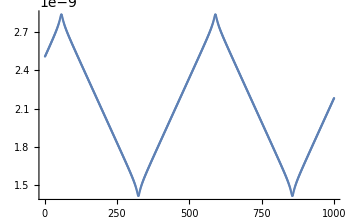

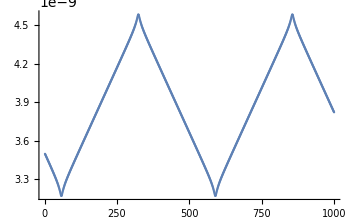

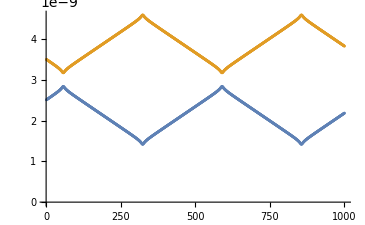

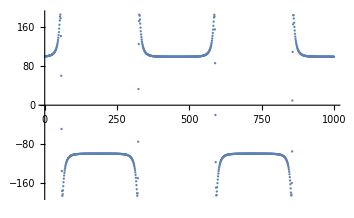

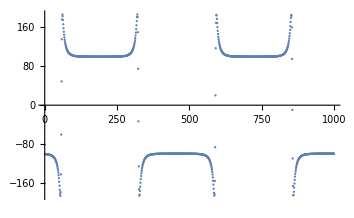

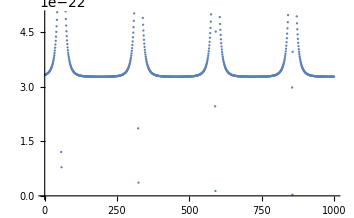

-Graphics-

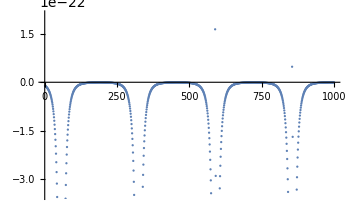

-Graphics-

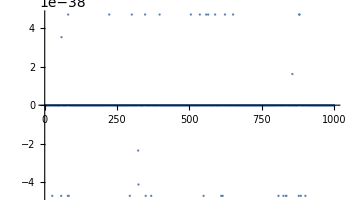

```mathematica
verlet= ReadList["~/phd-stuff/courses/astrid_sim/periodicverlet.txt",Number,RecordLists->True];

xpos=Table[verlet[[1+3*i]][[1]],{i,0,Length[(verlet)]/3-1}];
v=Table[verlet[[1+3*i]][[2]],{i,0,Length[(verlet)]/3-1}];
kin=Table[verlet[[1+3*i]][[3]],{i,0,Length[(verlet)]/3-1}];
pot=Table[verlet[[1+3*i]][[4]],{i,0,Length[(verlet)]/3-1}];

xpos2=Table[verlet[[2+3*i]][[1]],{i,0,Length[(verlet)]/3-1}];
v2=Table[verlet[[2+3*i]][[2]],{i,0,Length[(verlet)]/3-1}];
kin2=Table[verlet[[2+3*i]][[3]],{i,0,Length[(verlet)]/3-1}];
pot2=Table[verlet[[2+3*i]][[4]],{i,0,Length[(verlet)]/3-1}];

ListPlot[{xpos}]
ListPlot[{xpos2}]

ListPlot[{xpos,xpos2}]

ListPlot[{v}]
ListPlot[{v2}]

ListPlot[{kin}]
ListPlot[{kin2}]

ListPlot[{pot}]
ListPlot[{pot2}]

ListPlot[{kin+pot-(kin2+pot2)}]

k=650;
xpos[[k]];
xpos2[[k]];
```

4 ϵ (-σ^6/r^6+σ^12/r^12)

4 ϵ ((6 σ^6)/r^7-(12 σ^12)/r^13)

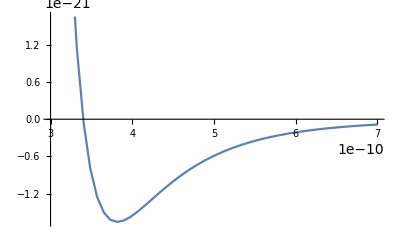

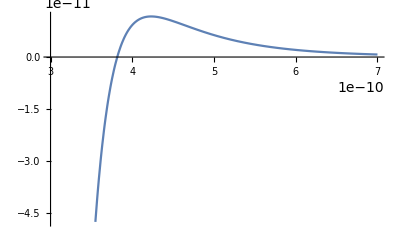

-Graphics-

```mathematica
T=120;
sigma=3.4*^-10;
kB=1.38064852*^-23;
epsilon=T*kB;
umass=1.660539040*^-27;
argonmass=umass*39.948;

min = 3*^-10;
max = 7*^-10;

4*ϵ*((σ/r)^12-(σ/r)^6)
D[%,r]

Plot[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Plot[24*epsilon*(sigma)^6*((r)^6-2*(sigma)^6)/(r)^13,{r,min,max}]
Plot[-24/r^2*epsilon*(2(sigma/r^12)-6(sigma/r^6)),{r,min,max}]

Manipulate[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Manipulate[24*epsilon*(sigma)^6*((r)^6-2*(sigma)^6)/(r)^13,{r,min,max}]
```

```mathematica
4*ϵ*((σ/r)^12-(σ/r)^6)
```

4 ϵ (-σ^6/r^6+σ^12/r^12)

```mathematica
scaleFactor=10^9;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/radialdistpos.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

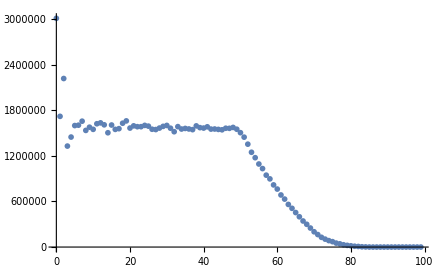

```mathematica
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->True];
ListPlot[rdf]
```

```mathematica
sigma=3.4*^-10;
boxlength=10.229*sigma
boxlength/5
Sqrt[3]*boxlength/2
a={boxlength/2,boxlength/2,boxlength/2};
b={0,0,0};
EuclideanDistance[a,b]
```

3.47786×10^-9

6.95572×10^-10

3.01192×10^-9

3.01192×10^-9